## Modeling Oscillations Lab Erin Murnane, Christopher Greene, Michael Imbimbo

## Below is the imported CSV file containing the Styrofoam ball’s actual data points from Logger Pro video analysis

```mathematica
smallballData ={{"VideoAnalysis: Time (s)","VideoAnalysis: X (m)","VideoAnalysis: Y (m)","VideoAnalysis: X Velocity (m/s)","VideoAnalysis: Y Velocity (m/s)"},{0,0.220059436445,0.218176723327,-0.238056175354,0.357531136627},{0.0212164486771,0.209754059378,0.226044482356,0.00694467214703,0.289216121607},{0.0464293475205,0.220118890543,0.236865128277,0.121569184309,0.116488256771},{0.0716422463639,0.221942149563,0.234486964338,0.0303685994868,-0.116478554121},{0.0968551452073,0.218632538081,0.225192306945,0.0244241682073,-0.15299698529},{0.122068044051,0.224181587271,0.224498675796,-0.0245142338627,-0.110967437774},{0.147280942894,0.21778036267,0.222041239727,-0.0834269978872,-0.0915820336011},{0.155685242509,0.21778036267,0.222041239727,0.0587506458446,-0.114912313484},{0.180898141352,0.220475615134,0.21237003971,0.140353950672,0.143663999973},{0.206111040195,0.225549031536,0.231117898759,0.199292291783,0.308581311229},{0.231323939039,0.229314457772,0.227352472523,0.290501742092,0.485014081884},{0.273345437111,0.240135103692,0.254086998798,0.480281073205,0.889079959869},{0.298558335955,0.261637669303,0.284884221802,0.723016202495,1.48624332808},{0.323771234798,0.283754593931,0.331734051391,0.73558422139,2.18715437754},{0.348984133642,0.296121046412,0.390058521983,0.789768875646,3.07945168353},{0.374197032485,0.32765153663,0.4886730533,0.672181747928,3.87542155985},{0.399409931328,0.33460766615,0.599436038737,0.372138485699,4.21129081188},{0.416218530557,0.337283100581,0.668700063447,0.284410964414,4.35509038176},{0.441431429401,0.345269767808,0.785804819386,0.248981708855,4.29621754294},{0.45824002863,0.348559561256,0.849935973595,0.2183275466,4.16403211234},{0.475048627859,0.352562803886,0.923084332737,0.184867630733,4.13618271996},{0.491857227088,0.352840256345,0.992348357446,0.242456744537,3.91736474592},{0.508665826316,0.361679098983,1.05564715428,0.25408340188,3.65188394473},{0.525474425545,0.363403267839,1.11460580192,0.169945704093,3.40051888809},{0.542283024774,0.365404889154,1.16916484628,0.172598547036,3.19503818902},{0.559091624003,0.368714500635,1.2211673644,0.179934804064,3.03105319376},{0.575900223232,0.374243731792,1.27265461367,0.059435774656,2.77203948453},{0.592708822461,0.371786295722,1.31562010882,-0.097047888194,2.45819039717},{0.60951742169,0.365860703909,1.35531562856,0.0176856196204,2.21554962237},{0.634730320534,0.370934120311,1.40587143029,0.148224249894,2.11363698366},{0.659943219377,0.378009158028,1.46197628121,0.121660880069,1.99461423478},{0.68515611822,0.378464972783,1.51675332392,0.0350000595698,1.53908558894},{0.710369017064,0.377216436715,1.5395638797,0.0303930648292,1.07238173785},{0.735581915907,0.379891871146,1.56094753711,0.0276201343455,0.94749069559},{0.760794814751,0.377890249831,1.58877205519,0.0522926654209,0.790896542605},{0.786007713594,0.38603546132,1.60109887161,-0.0410354640043,0.620155043087},{0.811220612437,0.37430318589,1.62606959296,-0.085019099546,0.229108312585},{0.836433511281,0.379376602293,1.61374277655,-0.0353212193066,-0.141632124457},{0.870050709739,0.373609554742,1.61221678802,-0.0258004607442,-0.283042859664},{0.912072207811,0.373609554742,1.5950543716,0.0493946851015,-0.469664852561},{0.945689406269,0.381695312133,1.57999266666,0.0387925006641,-0.743872303324},{0.970902305112,0.379376602293,1.55086015841,-0.092343777095,-1.13419567665},{0.996115203956,0.36980449244,1.51427606982,0.00158141254807,-1.26150869729},{1.0213281028,0.379198239997,1.49249605175,0.0734851531434,-1.54113331545},{1.06334960087,0.383478935087,1.41542372211,-0.0468682956147,-1.85879371262},{1.08856249972,0.371806113755,1.36572009579,-0.0977038140567,-2.20130114949},{1.11377539856,0.374877908842,1.29609934649,-0.0230345558257,-2.30093954226},{1.1389882974,0.373054649823,1.25041878084,0.00264180913403,-2.40216194755},{1.15579689663,0.37458063835,1.19587955452,0.0407343009339,-2.53063121321},{1.18100979547,0.376007536713,1.14177632492,0.011301772966,-2.57882184704},{1.20622269432,0.375789538352,1.07062958709,-0.022966742146,-2.77448889246},{1.23143559316,0.373787917037,1.00142501648,-0.0229957715721,-2.9628370197},{1.256648492,0.372024112116,0.919675631092,0.078890963966,-3.15375209255},{1.27345709123,0.379099149833,0.871279994943,0.139168982965,-3.4760430341},{1.29026569046,0.377156982617,0.79995489482,0.167635488539,-3.70572683113},{1.30707428969,0.383776205579,0.739648620946,0.208592058079,-3.57711307511},{1.32388288892,0.389067620342,0.688161371677,-0.00163755737226,-3.77784485781},{1.34069148815,0.382686213774,0.608017246949,-0.171124745401,-3.62977692021},{1.35750008738,0.380288231802,0.551060220621,-0.177478468006,-2.68048491151},{1.37430868661,0.378524426881,0.516636297611,-0.23626677767,-1.61643288216},{1.39111728584,0.368377594077,0.506489464807,-0.0898822490487,-1.07573763876},{1.40792588507,0.375908446549,0.485105807393,0.0292467746686,-0.814390032373},{1.42473448429,0.373629372775,0.479913482794,-0.0318996176116,-0.539345896128}};
```

```mathematica
Data1 = Table[{smallballData[[n,1]],smallballData[[n,3]]},{n,19,58}]
```

{{0.416219,0.6687},{0.441431,0.785805},{0.45824,0.849936},{0.475049,0.923084},{0.491857,0.992348},{0.508666,1.05565},{0.525474,1.11461},{0.542283,1.16916},{0.559092,1.22117},{0.5759,1.27265},{0.592709,1.31562},{0.609517,1.35532},{0.63473,1.40587},{0.659943,1.46198},{0.685156,1.51675},{0.710369,1.53956},{0.735582,1.56095},{0.760795,1.58877},{0.786008,1.6011},{0.811221,1.62607},{0.836434,1.61374},{0.870051,1.61222},{0.912072,1.59505},{0.945689,1.57999},{0.970902,1.55086},{0.996115,1.51428},{1.02133,1.4925},{1.06335,1.41542},{1.08856,1.36572},{1.11378,1.2961},{1.13899,1.25042},{1.1558,1.19588},{1.18101,1.14178},{1.20622,1.07063},{1.23144,1.00143},{1.25665,0.919676},{1.27346,0.87128},{1.29027,0.799955},{1.30707,0.739649},{1.32388,0.688161}}

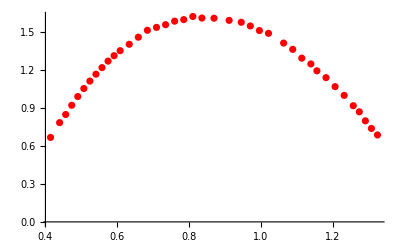

```mathematica
Experiment1= ListPlot[Data1,PlotStyle->Red]
```

## Styrofoam ball approximated model with just the force due to gravity

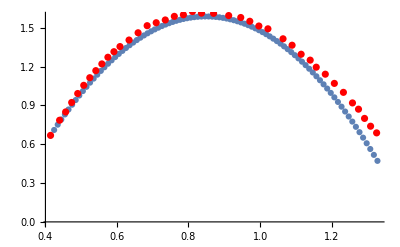

```mathematica
(* define constants and initial conditions *)

m = 0.0101;
g = 9.81;
x=0.668700063447;
vx=4.29621754294;
ti = 0.416218530557;
tf = 1.32388288892;
dt = .01;
(* define an array where we store the results of the simulation *) 
modeldata ={{ti,x}};

(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<=tf,
(* calculate the acceleration *)
ax = (-g*m)/m;

(* redefine y, vy, in terms of the values from the previous step *)
vx = vx + ax dt;
x = x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata = Append[modeldata,{t,x}];

];
(* plot the simulation and compare with the exact result *)
dataplot = ListPlot[modeldata];
Show[{dataplot,Experiment1}]
```

## Styrofoam ball approximated model with gravity and drag force one (1.2 from report).

0.0000155

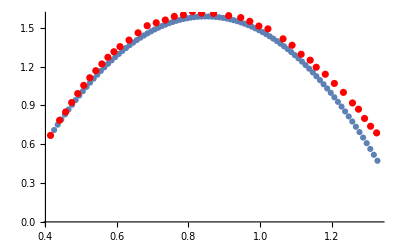

```mathematica
(* define constants and initial conditions *)

m = 0.0101;
smalld = .1;
c1 = 1.55*10^-4*smalld
g = 9.81;
x=0.668700063447;
vx=4.29621754294;
ti = 0.416218530557;
tf = 1.32388288892;
dt = .01;
(* define an array where we store the results of the simulation *) 
modeldata1 ={{ti,x}};

(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<=tf,
(* calculate the acceleration *)
drag = c1*vx;
ax = ((-g*m)+(drag))/m;

(* redefine y, vy, in terms of the values from the previous step *)
vx = vx + ax dt;
x = x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata1 = Append[modeldata1,{t,x}];

];
(* plot the simulation and compare with the exact result *)
dataplot1 = ListPlot[modeldata1];
Show[{dataplot1,Experiment1}]
```

## Styrofoam ball approximated model with gravity and drag force two (1.3 from report).

0.0022

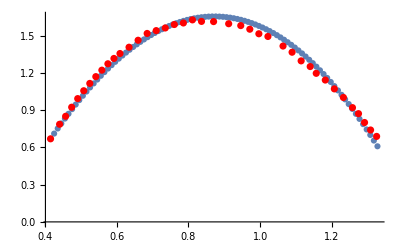

```mathematica
(* define constants and initial conditions *)

m = 0.0101;
smalld = .1;
c1 =0.22*smalld^2
g = 9.81;
x=0.668700063447;
vx=4.29621754294;
ti = 0.416218530557;
tf = 1.32388288892;
dt = .01;
(* define an array where we store the results of the simulation *) 
modeldata1 ={{ti,x}};

(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<=tf,
(* calculate the acceleration *)
drag = c1*vx;
ax = ((-g*m)+(drag))/m;

(* redefine y, vy, in terms of the values from the previous step *)
vx = vx + ax dt;
x = x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata1 = Append[modeldata1,{t,x}];

];
(* plot the simulation and compare with the exact result *)
dataplot1 = ListPlot[modeldata1];
Show[{dataplot1,Experiment1}]
```

## Styrofoam ball approximated model with gravity and drag force three (1.4 from report).

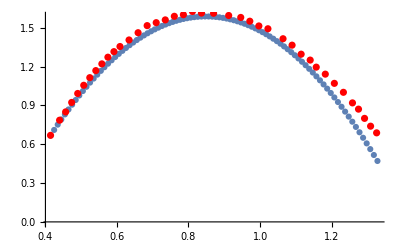

```mathematica
(* define constants and initial conditions *)

m = 0.0101;
smallr = .1/2;
viscosityair =1.983*10^-5; 
g = 9.81;
x=0.668700063447;
vx=4.29621754294;
ti = 0.416218530557;
tf = 1.32388288892;
dt = .01;
(* define an array where we store the results of the simulation *) 
modeldata1 ={{ti,x}};

(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<=tf,
(* calculate the acceleration *)
drag = -6π*smallr* viscosityair *vx;
ax = ((-g*m)+(drag))/m;

(* redefine y, vy, in terms of the values from the previous step *)
vx = vx + ax dt;
x = x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata1 = Append[modeldata1,{t,x}];

];
(* plot the simulation and compare with the exact result *)
dataplot1 = ListPlot[modeldata1];
Show[{dataplot1,Experiment1}]
```

## Below is the imported CSV file containing the beach ball’s actual data points from Logger Pro video analysis

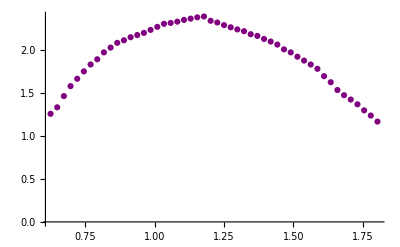

```mathematica
beachballdata = {{"VideoAnalysis: Time (s)","VideoAnalysis: X (m)","VideoAnalysis: Y (m)","VideoAnalysis: X Velocity (m/s)","VideoAnalysis: Y Velocity (m/s)"},{0.52914720141,1.13842495551,0.852253559033,0.782414107406,3.52670239458},{0.553166593213,1.15357164199,0.927986991411,0.907950699266,3.96170128265},{0.577185985015,1.18386501494,1.03906269223,0.900360114642,4.24605626049},{0.601205376818,1.20406059691,1.13499170658,0.642280237423,4.44341146072},{0.625224768621,1.21415838789,1.26121409388,0.385368142454,4.34998888073},{0.649244160423,1.21920728338,1.33694752626,0.245234272471,4.44341146072},{0.673263552226,1.22425617888,1.46821880904,0.186845159978,4.71200137818},{0.697282944028,1.22930507437,1.58434340536,0.105071256508,4.22042528602},{0.721302335831,1.22930507437,1.67017462872,0.0291314429656,3.70928032148},{0.745321727633,1.22930507437,1.75600585208,0.00582919592276,3.39760695371},{0.769581313354,1.22930507437,1.83678817995,0.0116583918455,3.04873976423},{0.793600705156,1.22930507437,1.89737492586,0.0349461022402,2.91624670802},{0.817620096959,1.22930507437,1.97815725373,0.105100402487,2.71439422741},{0.841639488762,1.23940286535,2.03369510414,0.0058389112493,2.29469212097},{0.865658880564,1.22930507437,2.08923295455,-0.0817447574902,1.83341813228},{0.889678272367,1.22930507437,2.1195263275,0.0467112899944,1.45388890108},{0.913697664169,1.23435396986,2.15486859594,0.0817447574902,1.27288265235},{0.937717055972,1.23435396986,2.1801130734,0.0700669349916,1.16158387153},{0.961736447774,1.23940286535,2.20535755086,-0.0174730511201,1.27146508687},{0.985755839577,1.23435396986,2.24069981931,-0.127879761956,1.37870539896},{1.0100154253,1.22930507437,2.27604208775,-0.0930640556194,1.31462785376},{1.0340348171,1.22930507437,2.31138435619,-0.0291314429656,0.979815660158},{1.0580542089,1.22930507437,2.32148214718,-0.00582919592276,0.694577840177},{1.08207360071,1.22930507437,2.33662883365,0,0.706508261165},{1.10609299251,1.22930507437,2.35682441562,0,0.694830438667},{1.13011238431,1.22930507437,2.3719711021,0.0058389112493,0.554696568683},{1.15413177611,1.22930507437,2.38711778857,0.0175167337479,0.216039716224},{1.17815116792,1.22930507437,2.39721557955,0.0583793971664,-0.648002564754},{1.20217055972,1.23435396986,2.34672662464,0.0233022470429,-1.16680165603},{1.22618995152,1.22930507437,2.32653104267,0.0291314429656,-1.1229313384},{1.25044953724,1.23435396986,2.29623766972,0.081420200422,-1.1228300158},{1.27446892904,1.23435396986,2.27099319226,0.0933254994066,-1.05566810844},{1.29848832085,1.23940286535,2.2457487148,0.0817253268371,-1.0215082935},{1.32250771265,1.23940286535,2.22555313283,0.0291945562465,-1.11523204862},{1.34652710445,1.23940286535,2.19021086439,0.0175167337479,-1.15610442736},{1.37054649625,1.23940286535,2.17001528242,0.0291945562465,-1.20281571736},{1.39456588806,1.24445176084,2.13467301398,-0.0700669349916,-1.34878849859},{1.41858527986,1.23435396986,2.10437964102,-0.0992712065646,-1.47099759111},{1.44260467166,1.23435396986,2.06903737258,0.0525502012437,-1.7673696114},{1.46662406346,1.23940286535,2.01349952217,0.122050566033,-1.84421421956},{1.49088364918,1.24445176084,1.97815725373,0.0466044940857,-1.84435915211},{1.51490304099,1.23940286535,1.92766829881,0.0349606388884,-1.93644558451},{1.53892243279,1.24445176084,1.88222823938,0.0817253268371,-1.97294965202},{1.56294182459,1.24445176084,1.83678817995,0.0934225799888,-2.18959171849},{1.58696121639,1.24950065634,1.78629922503,0.0875836687395,-2.74428828717},{1.6109806082,1.24950065634,1.70046800167,0.0525502012437,-3.12965642962},{1.635,1.24950065634,1.62978346479,0.110939313737,-3.22307900961},{1.6590193918,1.25454955183,1.53890334593,0.180967387422,-3.00040372536},{1.68303878361,1.25959844732,1.47831660003,0.204138586582,-2.50773651238},{1.70705817541,1.26464734281,1.42782764511,0.20944489493,-2.36814539528},{1.73131776113,1.2696962383,1.3722897947,0.197786503084,-2.55398364142},{1.75533715293,1.2747451338,1.30160525781,0.151704896573,-2.68296214182},{1.77935654473,1.27979402929,1.24101851191,0.0174875877683,-2.71436508143},{1.80337593654,1.2747451338,1.17033397502,-0.0700669349916,-2.65670461843},{1.82739532834,1.2696962383,1.10974722912,0.0840803219899,-2.44883937796},{1.85141472014,1.27979402929,1.04916048322,0.213120260599,-2.11660532787},{1.87543411194,1.28484292478,1.01381821477,0.233556449972,-1.76335119729}};
Data2 = Table[{beachballdata[[n,1]],beachballdata[[n,3]]},{n,6,55}];
Experiment2 = ListPlot[Data2, PlotStyle->Purple]
```

## Beach ball approximated model with just the force due to gravity

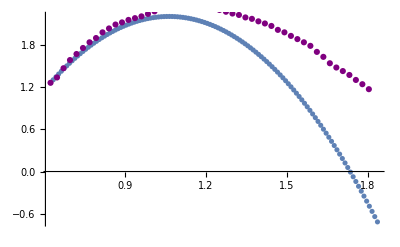

```mathematica
(* define constants and initial conditions *)

m = 0.1056;
g = 9.81;
x=1.26121409388;
vx=4.34998888073;
ti = 0.625224768621;
tf = 1.82739532834;
dt = .01;
(* define an array where we store the results of the simulation *) 
modeldata ={{ti,x}};

(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<=tf,
(* calculate the acceleration *)
ax = (-g*m)/m;

(* redefine y, vy, in terms of the values from the previous step *)
vx = vx + ax dt;
x = x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata = Append[modeldata,{t,x}];

];
(* plot the simulation and compare with the exact result *)
dataplot = ListPlot[modeldata];
Show[{dataplot,Experiment2}]
```

## Beach ball approximated model with the force due to gravity and drag force one (1.2 from the report)

0.00006975

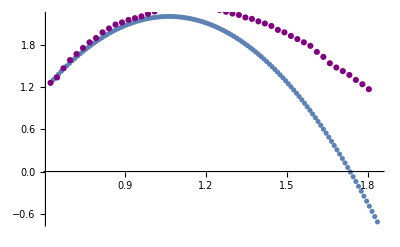

```mathematica
(* define constants and initial conditions *)

m = 0.1056;
bigd= .45;
c1 = 1.55*10^-4*bigd
g = 9.81;
x=1.26121409388;
vx=4.34998888073;
ti = 0.625224768621;
tf = 1.82739532834;
dt = .01;
(* define an array where we store the results of the simulation *) 
modeldata1 ={{ti,x}};

(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<=tf,
(* calculate the acceleration *)
drag = c1 * vx;
ax = ((-g*m)+(drag))/m;

(* redefine y, vy, in terms of the values from the previous step *)
vx = vx + ax dt;
x = x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata1 = Append[modeldata1,{t,x}];

];
(* plot the simulation and compare with the exact result *)
dataplot1 = ListPlot[modeldata1];
Show[{dataplot1,Experiment2}]
```

## Beach ball approximated model with the force due to gravity and drag force two (1.3 from the report)

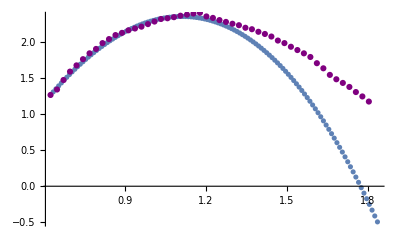

```mathematica
(* define constants and initial conditions *)

m = 0.1056;
bigd= .45;
c2 =0.22*(bigd^2);
g = 9.81;
x=1.26121409388;
vx=4.34998888073;
ti = 0.625224768621;
tf = 1.82739532834;
dt = .01;
(* define an array where we store the results of the simulation *) 
modeldata1 ={{ti,x}};

(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<=tf,
(* calculate the acceleration *)
drag = c2 * vx;
ax = ((-g*m)+(drag))/m;

(* redefine y, vy, in terms of the values from the previous step *)
vx = vx + ax dt;
x = x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata1 = Append[modeldata1,{t,x}];

];
(* plot the simulation and compare with the exact result *)
dataplot1 = ListPlot[modeldata1];
Show[{dataplot1,Experiment2}]
```

## Beach ball approximated model with the force due to gravity and drag force three (1.4 from report)

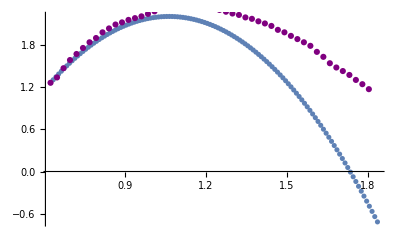

```mathematica
(* define constants and initial conditions *)

m = 0.1056;
bigr = .45/2;
viscosityair =1.983*10^-5; 
g = 9.81;
x=1.26121409388;
vx=4.34998888073;
ti = 0.625224768621;
tf = 1.82739532834;
dt = .01;
(* define an array where we store the results of the simulation *) 
modeldata1 ={{ti,x}};

(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<=tf,
(* calculate the acceleration *)
drag = -6π*bigr* viscosityair *vx;
ax = ((-g*m)+(drag))/m;

(* redefine y, vy, in terms of the values from the previous step *)
vx = vx + ax dt;
x = x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata1 = Append[modeldata1,{t,x}];

];
(* plot the simulation and compare with the exact result *)
dataplot1 = ListPlot[modeldata1];
Show[{dataplot1,Experiment2}]
```

## Most Accurate Approximation? For both balls, when combining the negative force due to gravity and the positive drag force equation 1.4, 0.22* D^2, our approximation was most accurate to the actual results.

#### Force due to Gravity without drag:

The styrofoam ball data seems considerably accurate when compared to the simulation.  When comparing the beachball data to the simulation, we see accuracy diminish immensely.  Although our simulations seem in favor of only one model and not both, drag must be taken into account.

#### Force due to Gravity with Drag Force One:

F(g) + F(v) = m dv/dt
F(g) is our constant force which does not depend on the velocity of the body.  When dealing with spheres, approximate values for constants were found so that c1 = 0.000155 * D and c2 = 0.22 * D^2, where D is the diameter of the sphere.

Force of Drag One:  -mg - c1*v = m dv/dt  , we then found acceleration by dividing Drag Force One by the inertia of the ball.
Because air is a resisting fluid, we must take into account how the ball is deccelerated upon it's accension and decension due to the force of this resisting fluid.  

c1 = 1.55*10^-4*D

When taking into account drag dealing with c1, it seems as if the amount of drag computed does not let either ball achieve its maximum ascension.  The styrofoam ball simulation and data seem to be very accurate to one another, yet the beach ball data and simulation prove to be quite different.  Due to the force of drag dealing with c1 only complimenting the styrofoam ball and not the beach ball, this drag force proves to be ineffective for varying cases

#### Force due to Gravity with Drag Force Three:

(C3) = -6π * D/2 * viscosity of air * velocity
Viscosity of air = 1.983*10^-5

Force of Drag Three:  -mg - c3*v = m dv/dt 
Drag Force Three depends on a different constant that now takes into account the viscosity of the air.  Once again, the data and simulation from the styrofoam ball seem accurate to one another, but the beach ball data and simulation evidently differentiate.  When taking account the viscosity of the air, the simulation of both balls prove to never reach their peak.  This is most likely due to the value for air resistance that c3 takes into account.  Both balls prove to deccelerate upon their accension and accelerate upon their decension too quickly.  Once again, the styrofoam ball data and simulation seem to fit rather well, but the beach ball data and simulation differ far too drastically.  Because this drag force only proves to be somewhat accurate for one model and not the other, this drag force proves to be inneffective for varying cases.

#### Force due to Gravity with Drag Force Two:

Drag Force Two deals with a different constant in which does not deal with the viscosity of air.  

C2 = 0.22 * D^2

Force of Drag Two:  -mg - c2*v = m dv/dt 
Out of the three models for each balls, the simulations dealing this new constant provide the most accurate models for both the styrofoam and the beach ball.  In both scenerios, from when the ball ascends to it’s peak, the data and model match up satisfyingly well.  Unlike the other two models dealing with C1 and C3, this new model allows both balls to reach the peak that was confirmed in the data found using Logger Pro.  When taking into account only the styrofoam ball, the data points taken after the ball begins to descend seem to not be as neat as the data points taken during its ascension to its peak.  I presume that if the data points taken after the ball reached it’s peak were to be recorded without the clutter of our other data points, the data and model would match up precisely.  In contrast, once the beach ball reached it’s peak and began to fall downward, the data and model seemed to stray from one another.